```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/yunqiguo/Document/CS249_2/project/249-Sun/src

```mathematica
purity[c_,w_]:=Module[{inter},
inter=Table[Length@Intersection[c[[i]],w[[j]]],{i,Length@c},{j,Length@w}];
Return@N[(Total@(Max/@inter))/(Total@(Length/@c))]
]
```

```mathematica
<<../data/edges3.mx
```

```mathematica
<<../data/top53.mx
```

```mathematica
g=Graph[edges];
```

```mathematica
distance=GraphDistanceMatrix[g];
```

```mathematica
vDic = Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[g];
```

```mathematica
Length/@top5
```

{946,1234,1243,1340,1441}

State of Art

```mathematica
communities0=FindGraphPartition[g,5];
```

```mathematica
purity[communities0,top5]
```

0.812122

```mathematica
pu={};
For[j=340,j≤520,j+=60,
Print[j];
communities=Select[FindGraphPartition[g,j],Length@#>0&];
communityDistanceMatrix=Table[N@Mean@Flatten@distance[[vDic/@communities[[i]],vDic/@communities[[j]]]],{i,Length@communities},{j,Length@communities}];
g2=WeightedAdjacencyGraph[1/(1+communityDistanceMatrix)];
(*Export["communityDistanceMatrix.csv",communityDistanceMatrix//TableForm];*)
communities4=FindGraphCommunities[g2,Method->"Spectral"];
Length@communities4
c4Size=Length@communities4;
distance2=GraphDistanceMatrix[g2];
vDic2= Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[g2];
communityDistanceMatrix2=Table[N@Mean@Flatten@distance2[[vDic2/@communities4[[i]],vDic2/@communities4[[j]]]],{i,c4Size},{j,c4Size}];
nearests=Position[#,Min[#]][[1,1]]&/@ communityDistanceMatrix2[[6;;,1;;5]];
communities5=Table[
Join[communities4[[i]],Flatten@ communities4[[ Position[nearests,i][[All,1]] +5]]],{i,5}];AppendTo[pu,purity[Flatten[communities[[#]]]&/@communities5,top5]];
]
```

340

400

460

520

```mathematica
pu
```

{0.946794,0.954005,0.949717,0.953225}

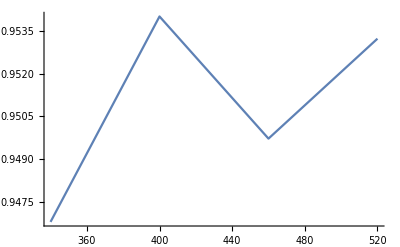

```mathematica
ListPlot[Transpose@{Range[340,520,60],pu},Joined->True,PlotStyle->PointSize[Large]]
```

r + Mathematica

```mathematica
communitiesFile=FileNames["../communities/*.txt"];
```

```mathematica
results={};
For[i=1,i≤Length@communitiesFile,i++,
Print[i];
clustering=Import[communitiesFile[[i]],"Data"];clustering=ToExpression/@StringSplit[clustering," "];communities=clustering;len1=Length@communities;
time1=Timing[communityDistanceMatrix=Table[N@Mean@Flatten@distance[[vDic/@communities[[i]],vDic/@communities[[j]]]],{i,Length@communities},{j,Length@communities}];
nearests=Position[#,Min[#]][[1,1]]&/@ communityDistanceMatrix[[6;;,1;;5]];communitiesFinal=Table[
Join[communities[[i]],Flatten@ communities[[ Position[nearests,i][[All,1]] +5]]],{i,5}];p1=purity[communitiesFinal,top5];
][[1]];
time2=Timing[g2=WeightedAdjacencyGraph[1/communityDistanceMatrix];
communities4=FindGraphCommunities[g2,Method->"Spectral"];len2=Length@communities4;c4Size=Length@communities4;distance2=GraphDistanceMatrix[g2];vDic2= Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[g2];communityDistanceMatrix2=Table[N@Mean@Flatten@distance2[[vDic2/@communities4[[i]],vDic2/@communities4[[j]]]],{i,c4Size},{j,c4Size}];nearests=Position[#,Min[#]][[1,1]]&/@ communityDistanceMatrix2[[6;;,1;;5]];communities5=Table[
Join[communities4[[i]],Flatten@ communities4[[ Position[nearests,i][[All,1]] +5]]],{i,5}];p2=purity[Flatten[communities[[#]]]&/@communities5,top5];
][[1]];
AppendTo[results,{communitiesFile[[i]],len1,p1,len2,p2,time1,time2}]
]
```

1

$Aborted

```mathematica
results[[All,1]]=StringDrop[StringDrop[results[[All,1]],15],-4]
```

{fast_greedy,infomap,label_prop,leading_eigen,louvain,optimal,springlass,walktrap}

```mathematica
Export["result.csv",results];
```